```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1/2}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1/2<x≤3/2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4]};
```

```mathematica
(*Continuity*)
C1=Limit[h[x],x->1/2,Direction->1]==Limit[h[x],x->1/2,Direction->-1]
C2=Limit[h[x],x->3/2,Direction->1]==Limit[h[x],x->3/2,Direction->-1]
```

1/16 (16+8 c_(0,1)+4 c_(0,2)+2 c_(0,3)+c_(0,4))==1/16 (-8 c_(1,1)+4 c_(1,2)-2 c_(1,3)+c_(1,4))

1/16 (8 c_(1,1)+4 c_(1,2)+2 c_(1,3)+c_(1,4))==0

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(i=-3)^3 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-3)^3 i f[x-i],x>0&&x<1/2],x]
```

{1,c_(0,1),c_(0,2)+2 c_(1,2),c_(0,3),c_(0,4)+2 c_(1,4)}

{0,-2 c_(1,1),0,-2 c_(1,3)}

```mathematica
GenSols=Solve[{
	C1,C2,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,3)→0,c_(0,4)→-8-4 c_(0,2),c_(1,1)→-1/2,c_(1,2)→-(c_(0,2))/2,c_(1,3)→0,c_(1,4)→4+2 c_(0,2)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]-1/2
```

{{-5/2,5/2},{-5/2,3/2},{-3/2,3/2},{-3/2,1/2},{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,-3/2},{3/2,-3/2},{3/2,-5/2},{5/2,-5/2},{5/2,-7/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

(9621843+4576290 c_(0,2)+979234 c_(0,2)^2+65410 c_(0,2)^3+2266 c_(0,2)^4)/16934400

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.183005 | True

```mathematica
RootReduce[Sols[[1]]]
```

{c_(0,2)→Root[2288145+979234 #1+98115 #1^2+4532 #1^3&,1]}

{c_(0,1)→0,c_(0,3)→0,c_(0,4)→4.8882,c_(1,1)→-1/2,c_(1,2)→1.61102,c_(1,3)→0,c_(1,4)→-2.4441,c_(0,2)→-3.22205}

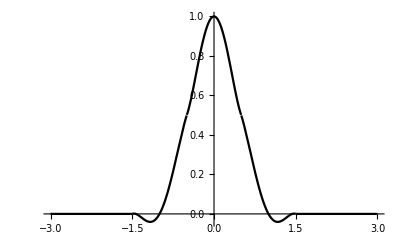

```mathematica
NSol=N[Sols[[1]]];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```